# Markov models of Introgression

## Discrete time model : try 1

```mathematica
mat2elem[AB_,Ab_,aB_,ab_]:=AB*3^3+Ab*3^2+aB*3+ab+1
```

```mathematica
elem2ab[i_]:=Mod[i-1,3]
elem2aB[i_]:=Mod[Floor[(i-1)/3],3]
elem2Ab[i_]:=Mod[Floor[(i-1)/3^2],3]
elem2AB[i_]:=Mod[Floor[(i-1)/3^3],3]
```

```mathematica
RandomInteger[MultinomialDistribution[1,{0.2,0.1,0.4,0.3}]]
```

{0,0,0,1}

```mathematica
PDF[MultinomialDistribution[1,{0.2,0.1,0.4,0.3}],{x1,x2,x3,x4}]
```

Piecewise[{{0.1^x2 0.2^x1 0.3^x4 0.4^x3 Binomial[1,x4] Binomial[x1+x2,x2] Binomial[x1+x2+x3,x3], x1+x2+x3+x4==1&&x1≥0&&x2≥0&&x3≥0&&x4≥0}, {0, True}}]

```mathematica
Clear[ABprime]
ABprime[y_,AB_,Ab_,aB_,ab_,pars_]:=
If[(AB+Ab)==0&&y≠0,0,If[(AB+Ab)==0&&y==0,1,
Sum[PDF[TruncatedDistribution[{-1,2},PoissonDistribution[(AB+Ab)sA]],x]PDF[BinomialDistribution[x,r(AB+aB)/(AB+Ab+aB+ab)+(1-r)AB/(AB+Ab+aB+ab)],y]//N,{x,0,2}]/.pars]];
Abprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(AB+Ab)==0&&y≠0,0,If[(AB+Ab)==0&&y==0,1,Sum[PDF[TruncatedDistribution[{-1,2},PoissonDistribution[(AB+Ab)sA]],x]PDF[BinomialDistribution[x,r(Ab+ab)/(AB+Ab+aB+ab)+(1-r)Ab/(AB+Ab+aB+ab)],y]//N,{x,0,2}]/.pars]];
aBprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(aB+ab)==0&&y≠0,0,If[(aB+ab)==0&&y==0,1,Sum[PDF[TruncatedDistribution[{-1,2},PoissonDistribution[(aB+ab)sa]],x]PDF[BinomialDistribution[x,r(AB+aB)/(AB+Ab+aB+ab)+(1-r)aB/(AB+Ab+aB+ab)],y]//N,{x,0,2}]/.pars]];
abprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(aB+ab)==0&&y≠0,0,If[(aB+ab)==0&&y==0,1,Sum[PDF[TruncatedDistribution[{-1,2},PoissonDistribution[(aB+ab)sA]],x]PDF[BinomialDistribution[x,r(Ab+ab)/(AB+Ab+aB+ab)+(1-r)ab/(AB+Ab+aB+ab)],y]//N,{x,0,2}]/.pars]];
new[ABp_,Abp_,aBp_,abp_,AB_,Ab_,aB_,ab_,pars_]:=ABprime[ABp,AB,Ab,aB,ab,pars]Abprime[Abp,AB,Ab,aB,ab,pars]aBprime[aBp,AB,Ab,aB,ab,pars]abprime[abp,AB,Ab,aB,ab,pars];
```

```mathematica
Sum[new[i,j,k,l,0,0,0,1,pars],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]//N
```

1.

```mathematica
MakeMatrix[pars_]:=Block[{out,AB,Ab,aB,ab,ABp,Abp,aBp,abp,r,sA,sa},
out=Table[0,{i,1,3^4},{j,1,3^4}];
(*From here*)
For[AB=0,AB≤2,++AB,
For[Ab=0,Ab≤2,++Ab,
For[aB=0,aB≤2,++aB,
For[ab=0,ab≤2,++ab,
(*To here*)
For[ABp=0,ABp≤2,++ABp,
For[Abp=0,Abp≤2,++Abp,
For[aBp=0,aBp≤2,++aBp,
For[abp=0,abp≤2,++abp,
If[AB==0&&Ab==0&&aB==0&&ab==0,out[[mat2elem[ABp,Abp,aBp,abp],mat2elem[AB,Ab,aB,ab]]]= 0,
out[[mat2elem[ABp,Abp,aBp,abp],mat2elem[AB,Ab,aB,ab]]]=new[ABp,Abp,aBp,abp,AB,Ab,aB,ab,pars];
]
]
]
]
]
]
]
]
];
out[[1,1]]=1; (*if AB=0,Ab=0,aB=0,ab=0 you stay*)
out
];
```

```mathematica
MakeInitVec[pars]:=Block[{out,i},
out =Table[0,{i,1,3^4}];
out[[mat2elem[0,2,2,0]]]=1;
out
]
```

```mathematica
Vector2Etypes[vec_]:=Block[{out},
out=Table[0,{i,1,4}];
For[i=1,i≤Length[vec],++i,
out[[1]]+=vec[[i]]*elem2AB[i];
out[[2]]+=vec[[i]]*elem2Ab[i];
out[[3]]+=vec[[i]]*elem2aB[i];
out[[4]]+=vec[[i]]*elem2ab[i];
];
out
]
```

## Without recombination

```mathematica
pars={r->0,sA->1,sa->1}
```

{r→0,sA→1,sa→1}

```mathematica
testmat=MakeMatrix[pars];
```

```mathematica
testinitvec=MakeInitVec[pars];
```

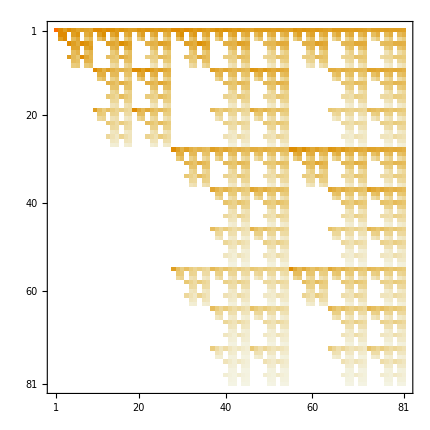

```mathematica
testmat//MatrixPlot
```

```mathematica
{MatrixPower[testmat,1].testinitvec}//Total//Total
```

1.

```mathematica
Vector2Etypes[MatrixPower[testmat,1].testinitvec]
```

{0.,0.6,0.6,0.}

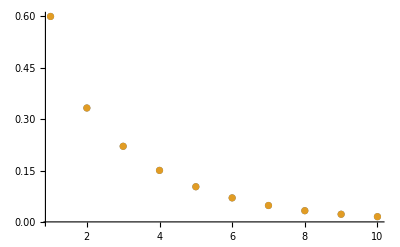

```mathematica
ListPlot[
{Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{2}]]//Flatten,
Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{3}]]//Flatten},PlotRange->All]
```

## With recombination

```mathematica
pars={r->1,sA->2,sa->0.5}
```

{r→1,sA→2,sa→0.5}

```mathematica
testmat=MakeMatrix[pars];
```

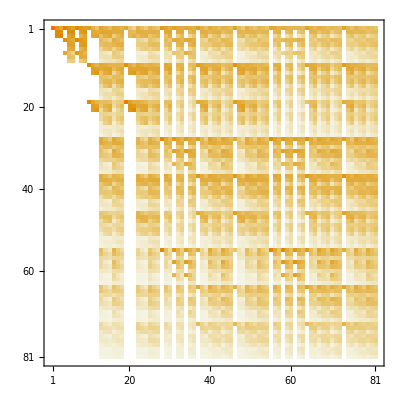

```mathematica
testmat//MatrixPlot
```

```mathematica
Vector2Etypes[MatrixPower[testmat,2].testinitvec]
```

{0.537251,0.678715,0.196443,0.6078}

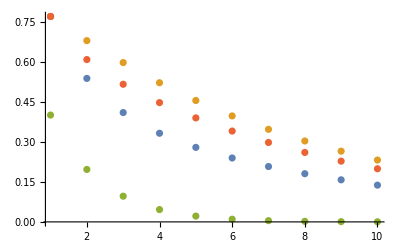

```mathematica
ListPlot[
{Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{1}]]//Flatten,
Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{2}]]//Flatten,
Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{3}]]//Flatten,
Table[Vector2Etypes[MatrixPower[testmat,t].testinitvec],{t,1,10}][[;;,{4}]]//Flatten},

PlotRange->All]
```

## Discrete time model : try 2

```mathematica
pars={r->1,sA->1,sa->1}
```

{r→1,sA→1,sa→1}

```mathematica
mat2elem[AB_,Ab_,aB_,ab_]:=AB*3^3+Ab*3^2+aB*3+ab+1
```

```mathematica
elem2ab[i_]:=Mod[i-1,3]
elem2aB[i_]:=Mod[Floor[(i-1)/3],3]
elem2Ab[i_]:=Mod[Floor[(i-1)/3^2],3]
elem2AB[i_]:=Mod[Floor[(i-1)/3^3],3]
```

```mathematica
Clear[ABprime]
ABprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(AB+Ab)==0&&y≠0,0,If[(AB+Ab)==0&&y==0,1,
Sum[N[PDF[TruncatedDistribution[{-1,10},PoissonDistribution[(AB+Ab)sA]],x]]PDF[BinomialDistribution[x,(AB+aB)/(AB+Ab+aB+ab)],y],{x,0,10}]/.pars]];
Abprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(AB+Ab)==0&&y≠0,0,If[(AB+Ab)==0&&y==0,1,
Sum[N[PDF[TruncatedDistribution[{-1,10},PoissonDistribution[(AB+Ab)sA]],x]]PDF[BinomialDistribution[x,(Ab+ab)/(AB+Ab+aB+ab)],y],{x,0,10}]/.pars]];
aBprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(aB+ab)==0&&y≠0,0,If[(aB+ab)==0&&y==0,1,
Sum[N[PDF[TruncatedDistribution[{-1,10},PoissonDistribution[(aB+ab)sa]],x]]PDF[BinomialDistribution[x,(AB+aB)/(AB+Ab+aB+ab)],y],{x,0,10}]/.pars]];
abprime[y_,AB_,Ab_,aB_,ab_,pars_]:=If[(aB+ab)==0&&y≠0,0,If[(aB+ab)==0&&y==0,1,
Sum[N[PDF[TruncatedDistribution[{-1,10},PoissonDistribution[(aB+ab)sa]],x]]PDF[BinomialDistribution[x,(Ab+ab)/(AB+Ab+aB+ab)],y],{x,0,10}]/.pars]];
new[ABp_,Abp_,aBp_,abp_,AB_,Ab_,aB_,ab_,pars_]:=ABprime[ABp,AB,Ab,aB,ab,pars]Abprime[Abp,AB,Ab,aB,ab,pars]aBprime[aBp,AB,Ab,aB,ab,pars]abprime[abp,AB,Ab,aB,ab,pars];
```

```mathematica
Sum[new[i,j,k,l,1,1,1,1,pars],{i,0,2},{j,0,2},{k,0,2},{l,0,2}]
```

0.715478

```mathematica
MakeMatrix[pars_]:=Block[{out,AB,Ab,aB,ab,ABp,Abp,aBp,abp,r,sA,sa},
out=Table[0,{i,1,3^4},{j,1,3^4}];
(*From here*)
For[AB=0,AB≤2,++AB,
For[Ab=0,Ab≤2,++Ab,
For[aB=0,aB≤2,++aB,
For[ab=0,ab≤2,++ab,
(*To here*)
For[ABp=0,ABp≤2,++ABp,
For[Abp=0,Abp≤2,++Abp,
For[aBp=0,aBp≤2,++aBp,
For[abp=0,abp≤2,++abp,
If[AB==0&&Ab==0&&aB==0&&ab==0,out[[mat2elem[ABp,Abp,aBp,abp],mat2elem[AB,Ab,aB,ab]]]= 0,
out[[mat2elem[ABp,Abp,aBp,abp],mat2elem[AB,Ab,aB,ab]]]=new[ABp,Abp,aBp,abp,AB,Ab,aB,ab,pars];
]
]
]
]
]
]
]
]
];
out[[1,1]]=1; (*if AB=0,Ab=0,aB=0,ab=0 you stay*)
out
];
```

```mathematica
test=MakeMatrix[pars]
```

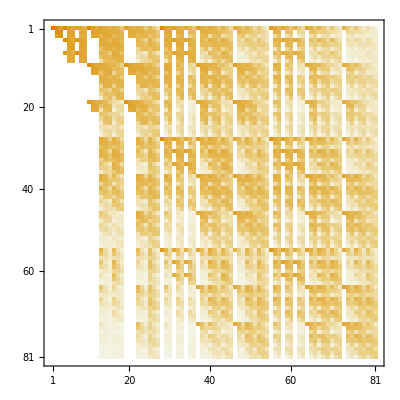

```mathematica
test//MatrixPlot
```

```mathematica
test//Total//N
```

{1.,0.919699,0.676682,0.919699,0.845859,0.622659,0.676682,0.622659,0.460397,0.919699,0.845846,0.622344,0.943679,0.794985,0.560016,0.794985,0.635901,0.434807,0.676682,0.622344,0.457899,0.794985,0.635559,0.432695,0.715478,0.538636,0.352848,0.919699,0.943679,0.794985,0.845846,0.794985,0.635901,0.622344,0.560016,0.434807,0.845859,0.794985,0.635559,0.794985,0.715478,0.538636,0.635559,0.538636,0.389431,0.622659,0.560016,0.432695,0.635901,0.538636,0.387704,0.538636,0.428504,0.294715,0.676682,0.794985,0.715478,0.622344,0.635559,0.538636,0.457899,0.432695,0.352848,0.622659,0.635901,0.538636,0.560016,0.538636,0.428504,0.432695,0.387704,0.294715,0.460397,0.434807,0.352848,0.434807,0.389431,0.294715,0.352848,0.294715,0.211965}

```mathematica
MakeInitVec[pars]:=Block[{out,i},
out =Table[0,{i,1,3^4}];
out[[mat2elem[0,1,0,1]]]=1;
out
]
```

```mathematica
MatrixPower[test,200].MakeInitVec[pars]//Total
```

0.508326

```mathematica
Vector2Etypes[vec_]:=Block[{out},
out=Table[0,{i,1,4}];
For[i=1,i≤Length[vec],++i,
out[[1]]+=vec[[i]]*elem2AB[i];
out[[2]]+=vec[[i]]*elem2Ab[i];
out[[3]]+=vec[[i]]*elem2aB[i];
out[[4]]+=vec[[i]]*elem2ab[i];
];
out
]
```